```mathematica
FourierTransform[1,t,ω]
```

√(2 π) DiracDelta[ω]

```mathematica
FourierTransform[ DiracDelta[ω] + DiracDelta[ω+a], ω, t]
```

(1+ⅇ^(-ⅈ a t))/(√(2 π))

```mathematica
FourierTransform[Sin[a*t*n]/t^n,t,ω]
```

(Gamma[1-n] (-ⅈ (-ⅈ a n-ⅈ ω)^(-1+n)+ⅈ (ⅈ a n-ⅈ ω)^(-1+n)+ⅈ (-ⅈ a n+ⅈ ω)^(-1+n) Cos[n π]-ⅈ (ⅈ a n+ⅈ ω)^(-1+n) Cos[n π]+(-ⅈ a n+ⅈ ω)^(-1+n) Sin[n π]-(ⅈ a n+ⅈ ω)^(-1+n) Sin[n π]))/(2 √(2 π))

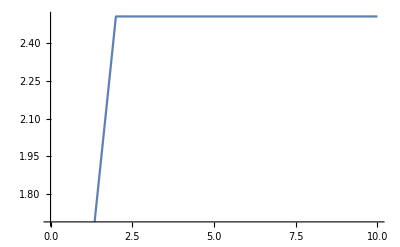

```mathematica
Plot[Abs[FourierTransform[Sin[2*a*t]/t^2,t,ω]/.a->1],{ω, 0, 10}]
```

```mathematica
func = (Gamma[1-n] (-ⅈ (-ⅈ a n-ⅈ ω)^(-1+n)+ⅈ (ⅈ a n-ⅈ ω)^(-1+n)+ⅈ (-ⅈ a n+ⅈ ω)^(-1+n) Cos[n π]-ⅈ (ⅈ a n+ⅈ ω)^(-1+n) Cos[n π]+(-ⅈ a n+ⅈ ω)^(-1+n) Sin[n π]-(ⅈ a n+ⅈ ω)^(-1+n) Sin[n π]))/(2 √(2 π))
```

(Gamma[1-n] (-ⅈ (-ⅈ a n-ⅈ ω)^(-1+n)+ⅈ (ⅈ a n-ⅈ ω)^(-1+n)+ⅈ (-ⅈ a n+ⅈ ω)^(-1+n) Cos[n π]-ⅈ (ⅈ a n+ⅈ ω)^(-1+n) Cos[n π]+(-ⅈ a n+ⅈ ω)^(-1+n) Sin[n π]-(ⅈ a n+ⅈ ω)^(-1+n) Sin[n π]))/(2 √(2 π))

```mathematica
Plot[Abs[func/.a->1/.n->2], {ω, 0 ,10}]
```

Infinity::indet: Indeterminate expression ((0.+0. ⅈ) ComplexInfinity)/(√(2 π)) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-